```mathematica
SetDirectory[NotebookDirectory[]];
curve1=Import["../data/out/curve1.csv"];
curve2=Import["../data/out/curve2.csv"];
matching=Import["../data/out/matching.csv"];
aStarPoints=Import["../data/out/debug_points.csv"];
```

```mathematica
ImageNorm=Norm[#,2]^2&;
ParamNorm=Norm[#,1]&;
```

```mathematica
(* Interpolating Line objects: *)
ClearAll[LineInterpolation,LineBreakPoints];

Options[LineBreakPoints]={Normalize->False};
LineBreakPoints[line_,opts:OptionsPattern[]]:=(
accum=Accumulate[#]&@Prepend[Norm[Subtract@@#]&/@Partition[line[[1]],2,1],0];
If[OptionValue[Normalize],accum/ArcLength[line],accum]);

LineInterpolation[line_,opts:OptionsPattern[{LineBreakPoints,Interpolation}]]:=(
breakpoints=LineBreakPoints[line,Sequence@@FilterRules[{opts},Options[LineBreakPoints]]];
Interpolation[Transpose[{breakpoints,line[[1]]}],InterpolationOrder->1,Sequence@@FilterRules[{opts},Options[Interpolation]]]);
```

```mathematica
c1=LineInterpolation[Line[curve1]];
c2=LineInterpolation[Line[curve2]];
m=LineInterpolation[Line[matching],Normalize->True];
```

```mathematica
len1=ArcLength@Line[curve1];
len2=ArcLength@Line[curve2];
```

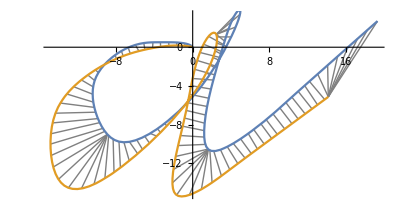

```mathematica
Show[
ListLinePlot[
Table[Quiet@({c1[#1],c2[#2]}&@@m[t]),{t,0,1,1/100}],
PlotStyle->Directive[Gray,Thin]
],
ParametricPlot[{c1[t len1],c2[t len2]},{t,0,1}],
AspectRatio->Automatic
]
```

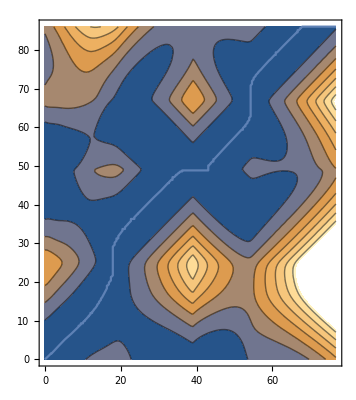

```mathematica
Show[
ContourPlot[ImageNorm[c1[t1]-c2[t2]],{t1,0,len1},{t2,0,len2}],
ParametricPlot[m[t],{t,0,1}],
AspectRatio->Automatic
]
```

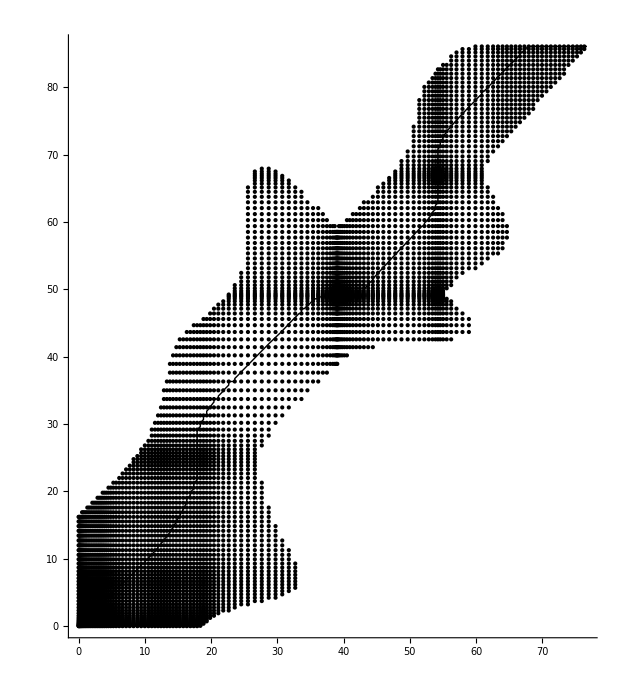

```mathematica
Show[
Graphics[{
(*PointSize[Small],*)
Point[aStarPoints,VertexColors->ColorData["DarkRainbow"]/@Rescale[Range[Length[aStarPoints]]]]
}],
ParametricPlot[m[t],{t,0,1},PlotStyle->Directive[Black,Thick]],
AspectRatio->Automatic,
Axes->True
]
```

```mathematica
ClearAll[Cost,Dist];
Cost[t_?NumericQ]:=ImageNorm[c1[#1]-c2[#2]]&@@m[t];
Dist[t_?NumericQ]:=ParamNorm[m'[t]];
NIntegrate[Cost[t]Dist[t],{t,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.230453}. NIntegrate obtained 1428.77 and 7.82803 for the integral and error estimates.

1428.77